```mathematica
(*WHITE DWARF MULTI SELF*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
ϵ=10^-4;
umin[N_]:=vesc*(Log[1/ϵ]^(N-1)-1)^0.5;
umax=∞;
```

```mathematica
gN[u_,N_]:=vesc^2/(u^2+vesc^2)*Log[1/ϵ]^(N-1);
```

```mathematica
sigmaSat[Nchi_]:=(π *R^2)/Nchi;
```

```mathematica
tau[sigmadmdm_,Nchi_]:=Min[(3*sigmadmdm)/(2*sigmaSat[Nchi]),3/2];
```

```mathematica
pn[N_,sigmadmdm_,Nchi_]:=2/(Factorial[N]*tau[sigmadmdm,Nchi]*tau[sigmadmdm,Nchi])*(Gamma[N+2]-Gamma[(N+2),tau[sigmadmdm,Nchi]]);
```

```mathematica
Cself[N_,mx_,sigmadmdm_,Nchi_]:= π R^2 pn[N,sigmadmdm,Nchi] ρx/mx*vesc^2*Log[1/ϵ]^(N-1)*(6/π)^0.5*1/vbar*Exp[(-3*umin[N]^2)/(2*vbar^2)];
```

```mathematica
Cself[1,10,10^-28,10^40]
```

2.46945×10^29

```mathematica
fMB[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2];
Integrate[fMB[u]/u,{u,umin,∞}]
```

ConditionalExpression[ⅇ^(-(3 umin^2)/(2 vbar^2)) √(6/π) √(1/vbar^2),Re[vbar^2]>0]

```mathematica
(*WHITE DWARF MULTI SELF WITH DIRAC DELTA OF Z*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;

umin=0;
umax[N_]:=vesc*((1/0.5)^N-1)^0.5;
```

```mathematica
sigmaSat[Nchi_]:=(π *R^2)/Nchi;
```

```mathematica
tau[sigmadmdm_,Nchi_]:=Min[(3*sigmadmdm)/(2*sigmaSat[Nchi]),3/2];
```

```mathematica
pn[N_,sigmadmdm_,Nchi_]:=2/(Factorial[N]*tau[sigmadmdm,Nchi]*tau[sigmadmdm,Nchi])*(Gamma[N+2]-Gamma[(N+2),tau[sigmadmdm,Nchi]]);
```

```mathematica
Cself[N_,mx_,sigmadmdm_,Nchi_]:= π R^2 pn[N,sigmadmdm,Nchi] ρx/mx* √(2/(3 π)) √(1/vbar^2) ((2 vbar^2+3 vesc^2)(*-(2 vbar^2+3 vesc^2+3*umax[N]^2)*ⅇ^(-(3 umax[N]^2)/(2 vbar^2))*));
```

```mathematica
Cself[1,10,10^-28,10^40]//N
```

2.46947×10^29

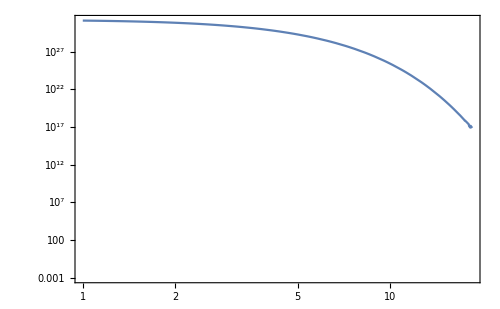

```mathematica
LogLogPlot[Cself[x,10,10^-28,10^45],{x,1,1000},Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotRange->{Automatic,{0.001,Automatic}}]
```

```mathematica
fMB[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2];
Integrate[fMB[u]/u*(u^2+vesc^2),{u,0,umax}]//FullSimplify
```

ⅇ^(-(3 umax^2)/(2 vbar^2)) √(2/(3 π)) √(1/vbar^2) (-3 umax^2+(-1+ⅇ^((3 umax^2)/(2 vbar^2))) (2 vbar^2+3 vesc^2))

```mathematica
(*SUN MULTI SELF*)
```

```mathematica
R=6.95*10^8;(*in m*)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=287.5*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)
ϵ=10^-4;
umin[N_]:=vesc*(Log[1/ϵ]^(N-1)-1)^0.5;
umax=∞;
```

```mathematica
gN[u_,N_]:=vesc^2/(u^2+vesc^2)*Log[1/ϵ]^(N-1);
```

```mathematica
sigmaSat[Nchi_]:=(π *R^2)/Nchi;
```

```mathematica
tau[sigmadmdm_,Nchi_]:=Min[(3*sigmadmdm)/(2*sigmaSat[Nchi]),3/2];
```

```mathematica
pn[N_,sigmadmdm_,Nchi_]:=2/(Factorial[N]*tau[sigmadmdm,Nchi]*tau[sigmadmdm,Nchi])*(Gamma[N+2]-Gamma[(N+2),tau[sigmadmdm,Nchi]]);
```

```mathematica
Cself[N_,mx_,sigmadmdm_,Nchi_]:= π R^2 pn[N,sigmadmdm,Nchi] ρx/mx*vesc^2*Log[1/ϵ]^(N-1)*(6/π)^0.5*1/vbar*Exp[(-3*umin[N]^2)/(2*vbar^2)];
```

```mathematica
Cself[3,10,10^-28,10^45]
```

1.94227×10^-226

```mathematica
(*SUN MULTI SELF WITH DIRAC DELTA OF Z*)
```

```mathematica
R=6.95*10^8;(*in m*)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=287.5*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)
ϵ=10^-4;
umin=0;
umax[N_]:=vesc*(2^N-1)^0.5;
```

```mathematica
sigmaSat[Nchi_]:=(π *R^2)/Nchi;
```

```mathematica
tau[sigmadmdm_,Nchi_]:=Min[(3*sigmadmdm)/(2*sigmaSat[Nchi]),3/2];
```

```mathematica
pn[N_,sigmadmdm_,Nchi_]:=2/(Factorial[N]*tau[sigmadmdm,Nchi]*tau[sigmadmdm,Nchi])*(Gamma[N+2]-Gamma[(N+2),tau[sigmadmdm,Nchi]]);
```

```mathematica
Cself[N_,mx_,sigmadmdm_,Nchi_]:= π R^2 pn[N,sigmadmdm,Nchi] ρx/mx*√(2/(3 π)) √(1/vbar^2) ((2 vbar^2+3 vesc^2)-(2 vbar^2+3 vesc^2+3*umax[N]^2)*ⅇ^(-(3 umax[N]^2)/(2 vbar^2)));
```

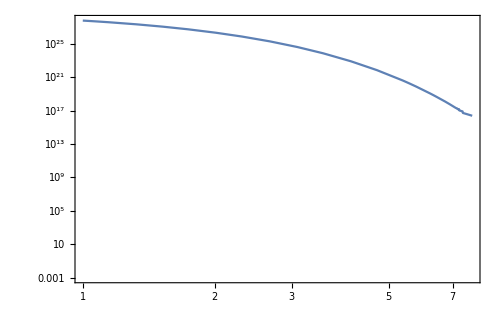

```mathematica
LogLogPlot[Cself[x,10,10^-28,10^45],{x,1,1000},Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotRange->{Automatic,{0.001,Automatic}}]//Quiet
```

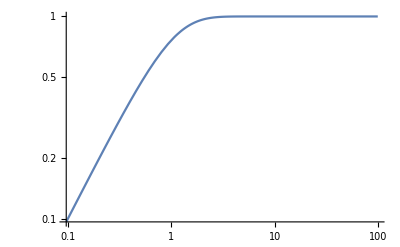

```mathematica
LogLogPlot[Tanh[x],{x,0,99},PlotRange->All]
```